```mathematica
ClearAll["Global`*"];
U1=9.;UD=2.5;ID=25.*10^-3;

IR1=ID
UR1=U1-UD
R1=UR1/IR1
```

0.025

6.5

260.

```mathematica
ClearAll["Global`*"];
R1=220.;UD=2.5;ID=25.*10^-3;

IR1=ID
UR1=ID*R1
U1=UR1+UD
```

0.025

5.5

8.

{c1→47/100000,r1→1000,uz[t]→12 Sin[100 π t]}

{iz[t]==id1[t],id1[t]==ic1[t]+ir1[t],id1[t]==(-1+ⅇ^(19 (u1[t]-u2[t])))/10000000,u2[t]==r1 ir1[t],ic1[t]==c1 u2'[t],uz[t]==u1[t],u2[0]==0}

{{iz[t]→InterpolatingFunction[{{0., 0.06}}, <>][t],id1[t]→InterpolatingFunction[{{0., 0.06}}, <>][t],ir1[t]→InterpolatingFunction[{{0., 0.06}}, <>][t],ic1[t]→InterpolatingFunction[{{0., 0.06}}, <>][t],u1[t]→InterpolatingFunction[{{0., 0.06}}, <>][t],u2[t]→InterpolatingFunction[{{0., 0.06}}, <>][t]}}

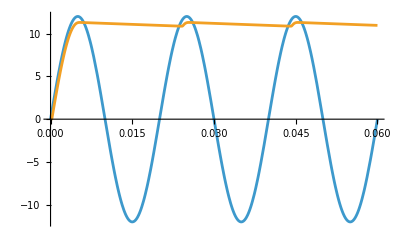

```mathematica
ClearAll["Global`*"];
suciastky={c1->470*10^-6,r1->1*10^3,uz[t]->12*Sin[2*Pi*50*t]}

rovnice={
iz[t]==id1[t],
id1[t]==ir1[t]+ic1[t],

id1[t]==10^-7*(E^(19*(u1[t]-u2[t]))-1),
u2[t]==r1*ir1[t],
ic1[t]==c1*u2'[t],
uz[t]==u1[t],

u2[0]==0
}
nezname={iz[t],id1[t],ir1[t],ic1[t],u1[t],u2[t]};

riesenie=NDSolve[rovnice/.suciastky,nezname,{t,0,3/50}]
Plot[{u1[t]/.riesenie,u2[t]/.riesenie},{t,0,3/50}]
```

```mathematica
ClearAll["Global`*"];
suciastky={U1->50.*10^-3,R1->1.*10^3,R2->100.*10^3,Aop->10.^5};

rovnice={
0==Iz+Ir1,
Ir1==Ir2,
Ir2+Io==0,

Uz==U1,
U1-U2==R1*Ir1,
U2-U3==R2*Ir2,
U3==Aop*(UP-UN),

UP==0,
UN==U2
}

riesenie=Solve[rovnice/.suciastky];
U3/.riesenie[[1]]//EngineeringForm
Ir1/.riesenie[[1]]//EngineeringForm
Ir2/.riesenie[[1]]//EngineeringForm
U3/U1/.riesenie[[1]]/.suciastky//EngineeringForm
```

{0==Ir1+Iz,Ir1==Ir2,Io+Ir2==0,Uz==U1,U1-U2==Ir1 R1,U2-U3==Ir2 R2,U3==Aop (-UN+UP),UP==0,UN==U2}

-4.99496

49.9501×10^-6

49.9501×10^-6

-99.8991